-Graphics-

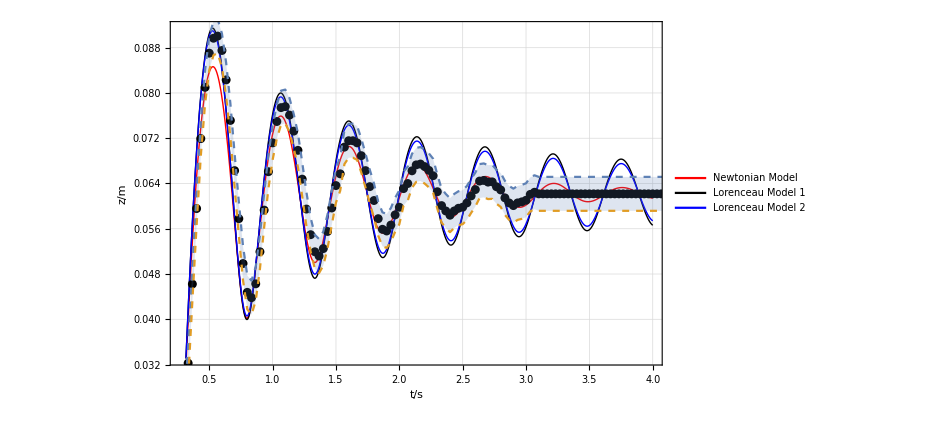

```mathematica
Clear[z,g,h,z0,t0,b,η,ρ,R,Ω,s1,s2,s3,data,data1,data2,style,F,m,c,fit,f1,f2,f3]
g=8.5;
h=6.22 0.01;(*m*)
z0=1.4 0.01;
t0=0.267;(*s*)
b=0.12;(*parameter of Newtonian Model*)
η=0.890*10^-3;(*/Pa s, water, CRC:6-247*)
ρ=997;(*/kg/m^3, water, CRC:6-7*)
R=(2.05/2)*0.01;(*tube radius*)
Ω=16η/ρ /R^2;
opts={PrecisionGoal->4,PrecisionGoal->4};
end=4;
s1=NDSolveValue[{z''[t]==-((z'[t])^2+g (z[t]-h)+b z'[t])/z[t],z'[0]==0,z[0]==z0},z,{t,0,end},opts];
s2=NDSolveValue[{z''[t]==-(If[z'[t]>0,1,0](z'[t])^2+g(z[t]-h))/z[t],z'[0]==0,z[0]==z0},z,{t,0,end},opts];
s3=NDSolveValue[{z''[t]==-(If[z'[t]>0,1,0](z'[t])^2+g(z[t]-h)+Ω z[t]z'[t])/z[t],z'[0]==0,z[0]==z0},z,{t,0,end},opts];
(*the data was obtained in Tracker*)
data1=Import["E:\\works\\nb\\miscellaneous\\liquid oscillation\\video\\2021_1_26.xlsx",{"Data","Sheet1",All,1}];
data2=Import["E:\\works\\nb\\miscellaneous\\liquid oscillation\\video\\2021_1_26.xlsx",{"Data","Sheet1",All,2}];
data=Table[{data1[[i]],data2[[i]]},{i,Length[data1]}];
datamax=Table[{data1[[i]],data2[[i]]+0.003},{i,Length[data1]}];
datamin=Table[{data1[[i]],data2[[i]]-0.003},{i,Length[data1]}];
style={LabelStyle->{Black,FontFamily->"Segoe UI Historic",FontSize->20}};
Show[Plot[{s1[t-t0],s2[t-t0],s3[t-t0]},{t,t0,end},PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick}},Evaluate[style],
PlotLegends->Placed[LineLegend[{"Newtonian Model","Lorenceau Model 1","Lorenceau Model 2"},LegendFunction->"Panel",LabelStyle->{Black,FontFamily->"Segoe UI Historic",FontSize-> 13,FontSlant->Plain,FontWeight-> Plain}],{0.7,0.8}]],
ListPlot[data,PlotStyle->Black],
ListLinePlot[{datamax,datamin},PlotStyle-> Dashed,Filling->{1->{2}}],
Frame->True,FrameStyle->Black,FrameLabel->{"t/s","z/m"},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.005],Opacity[0.5]],style,ImageSize->700]
```

natural frequency:

1.86052

frequency of fit maximum:

1.72408

frequency of maximum Fourier Component:

1.81818

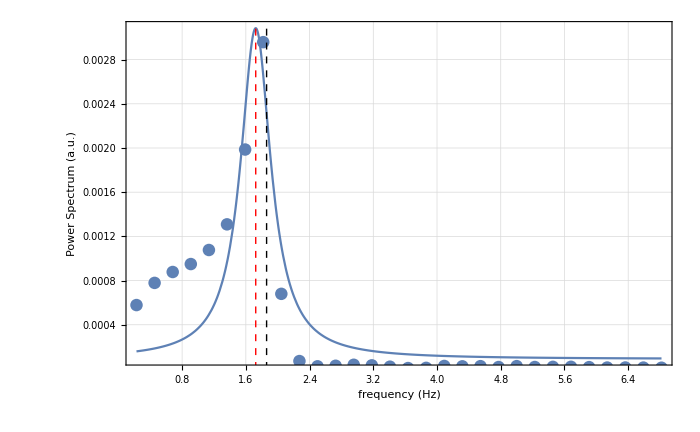

```mathematica
F=Abs[Fourier[data2]]^2;
m=30;
c=Table[{i*30/Length[F],F[[i+1]]},{i,1,m}];
fit=NonlinearModelFit[c,A B /((x-x0)^2+B^2)+y0,{A,B,x0,y0},x];
Print["natural frequency:"];
f1=Sqrt[g/h]/2/Pi
Print["frequency of fit maximum:"];
f2=x/.FindMaximum[fit[x],{x,0,3}][[2]]
Print["frequency of maximum Fourier Component:"];
f3=c[[(Position[#, Max[#]]&@c[[;;,2]])[[1,1]],1]]//N
Show[Plot[fit[x],{x,Min[c[[All,1]]],Max[c[[All,1]]]},PlotRange->Full],
ListPlot[c] ,
Graphics[{Red,Dashed,Line[{{f2,0},{f2,1}}]}],
Graphics[{Dashed,Line[{{f1,0},{f1,1}}]}],
Frame->True,FrameStyle->Black,FrameLabel->{"frequency (Hz)","Power Spectrum (a.u.)"},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.005],Opacity[0.5]],style,ImageSize->700]
```